```mathematica
ClearAll["Global`*"];
subTitle[text_]:=Style[text,FontFamily->"Calibri",16,Bold,Black];
txtF[text_]:=Style[text,FontFamily->"Calibri",14,Gray];
numericF[text_,size_,color_]:=Framed[Style[text,FontFamily->"Calibri",size,White],Background->color,ImageSize->{100,45},Alignment->Center];
numberF[text_]:=Style[text,FontFamily->"Cambria Math",20];
txtTitle[text_]:=Style[text,FontFamily->"Calibri",36,Bold];
txtinfo[text_]:=Style[text,FontFamily->"Calibri",20,Bold];
solar=Show[
{ParametricPlot3D[{0.5*Cos[x],0.5*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All,Boxed->False,ImageSize->{300,300}],
ParametricPlot3D[{1*Cos[x],1*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All ,Boxed->False],
ParametricPlot3D[{1.5*Cos[x],1.5*Sin[x],0},{x,0,2π},Axes->False,PlotRange->All,Boxed->False],
ParametricPlot3D[{2*Cos[x],2*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All,Boxed->False],
ParametricPlot3D[{2.5*Cos[x],2.5*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All,Boxed->False],
ParametricPlot3D[{3*Cos[x],3*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All ,Boxed->False],
ParametricPlot3D[{3.5*Cos[x],3.5*Sin[x],0},{x,0,2π},Axes->False,PlotRange->All,Boxed->False],
ParametricPlot3D[{4*Cos[x],4*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All,Boxed->False],
ParametricPlot3D[{4.5*Cos[x],4.5*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All,Boxed->False],
ParametricPlot3D[{5*Cos[x],5*Sin[x],0},{x,0,2π},Axes->False,PlotRange-> All ,Boxed->False],
Graphics3D[{{Gray,Sphere[{0,0,0.15},0.15],Gray,Sphere[{0,0.15*1,0.15*(-Sqrt[3]+1)},0.15*1],Gray,Sphere[{0,-0.15*1,0.15*(-Sqrt[3]+1)},0.15*1],Gray,Opacity[0.3],Sphere[{0,0,0.15*(1-2*Sqrt[3]/3)},0.15*(1+2*Sqrt[3]/3)]},Table[{{Blue,Red,Green,Orange,Gray,Yellow,Purple,Black,RGBColor[0.17,0.24,0.89],RGBColor[0.85,0.08,0.79]}[[i]],Sphere[{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}[[i]]{Cos[{1,2,3,4,5,6,7,8,9,10}[[i]]],Sin[{1,2,3,4,5,6,7,8,9,10}[[i]]],0},{0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12}[[i]]]},{i,10}]},PlotRange->All,ImageSize->{600,600},Boxed-> False,SphericalRegion-> True,ViewAngle->Pi/8]}
];
```

```mathematica
lectext={{"K","1s^2"," "," "," "},{"L","2s^2","2p^6"," "," "},{"M","3s^2","3p^6","3d^10"," "},{"N","4s^2","4p^6","4d^10","4f^14"}};
shelltable  = Grid[Prepend[lectext,{"SHELL"," "," "," "," "}],Background->{None,{Darker[RGBColor[0.37,0.42,1]],{Lighter[Blue,0.6],Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{White,{White},White},{White,White,White}},Alignment->{{Left,Right,{Left}}},ItemSize->{{10,6,6,6},{6,4,4,4}},Frame->Darker[Gray,.6],ItemStyle->20];
```

```mathematica
orbits=Manipulate[
If[l≥n,l=n-1];
If[m>l,m=l];
DensityPlot[Module[{r=Norm[{x,0,z}]},4 π r^2 (Exp[-r/n] r^l LaguerreL[n-1-l,2 l+1,(2 r)/n])^2 Abs[SphericalHarmonicY[l,m,ArcCos[z/r],ArcTan[x,0]]]^2],{x,-40,40},{z,-40,40},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"],
{{n,3, "principal quantum number"},1,5,1,ControlType->Setter},
{{l,2,"angular momentum"},Range[0,n-1],ControlType->SetterBar},
{{m,0,"magnetic quantum number"},Range[0,l],ControlType->SetterBar},
Paneled->False];
```

```mathematica
funnel = Grid[{{
Column[{
Show[{
Plot3D[{-1/Sqrt[(x^2+y^2)]},{x,-1,1},{y,-1,1},PlotRange->{{-1,1},{-1,1},{0,-20}},PlotStyle->{Opacity[0.4]},BoxRatios->{1, 1, 1},Axes-> False,Mesh->False,Background->Black,ImageSize->{620,620},ColorFunction->(Blend[{Red,Yellow},#3]&)], 
ParametricPlot3D[{
(* Marker 3D *)
{0.06*Cos[α],0.06*Sin[α],-1/0.06}},{α,0,2*π},PlotStyle->{RGBColor[0.42,0.55,0.83],Thick},PlotRange->{{-1,1},{-1,1},{0,-20}},Axes->True,Mesh->False,ImageSize->{620,620},SphericalRegion->True]}],
subTitle["Trap View"],
txtF["This view is designed to convey the idea that the nuclear potential."],
txtF["acts as a trap for electrons. The vertical dimension represents"],
txtF["potential energy."]
}]
}},Frame->True];
twoD = Grid[{{
Column[{
Show[{Plot[{-1/Sqrt[x^2]},{x,0,1},PlotRange-> {{0,1},{0,-20}},PlotStyle->Thick,Axes-> True,ImageSize->{620,620},Background->Black,ColorFunction->(Blend[{Red,Yellow},#1]&)],
(* Marker 2D *)
Graphics[{PointSize[Large],Thick,RGBColor[0.42,0.55,0.83],Point[{0.06,-1/0.06}]},ImageSize->{620,620},Background->Black]
}],
subTitle["Graph View"],
txtF["2-D function graph allows for indicating/presenting"],
txtF["sepecific potential energy, and r and V being inverse."],
txtF[" "]
}]
}},Frame->True];
```

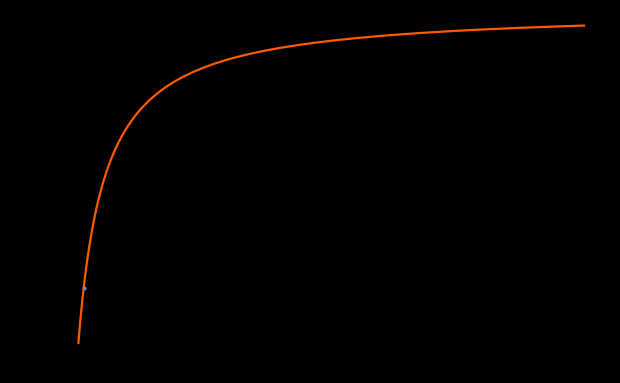
Representations of Electronic Structure
SHELL |   |   |   |  
K | 1s^2 |   |   |  
L | 2s^2 | 2p^6 |   |  
M | 3s^2 | 3p^6 | 3d^10 |  
N | 4s^2 | 4p^6 | 4d^10 | 4f^14-Graphics3D-
 
-Graphics3D-
Trap View
This view is designed to convey the idea that the nuclear potential.
acts as a trap for electrons. The vertical dimension represents
potential energy.-Graphics-
Graph View
2-D function graph allows for indicating/presenting
sepecific potential energy, and r and V being inverse.

```mathematica
mockupLayout = 
Framed[Grid[{{
txtTitle["Representations of Electronic Structure"]},
{Grid[{
{
Column[{
Framed[Row[{Column[{
Row[{shelltable,solar}],
" "
},Alignment->Center],orbits}]],
Row[{funnel,twoD}]
}]
}
}]
}},Alignment->Center],RoundingRadius->15]
```